```mathematica
Animating flow in relativistic phase space
Didi Park - Computational Physics, Period 6
```

```mathematica
(*Create 20 random points, pair the numbers using transpose. Rerun to get a new set of points.*)
r1 = RandomReal[{-4,4},{20}];
r2 = RandomReal[{-4,4},{20}];
pos = Transpose[{ r1,r2}];
```

```mathematica
(*Creates points with different initial conditions*)

(*Relativistic*)
relPoints = Function[{a,c,m, f,tf},NDSolve[{p'[t]==f[x[t]], x'[t]==(p[t]/m)/Sqrt[1+(p[t]/(m*c))^2],x[0]==a[[1]],p[0]==a[[2]]},{x,p},{t,0,tf}]];
(*Newtonian*)
newtPoints = Function[{a,c,m, f,tf},NDSolve[{p'[t]==f[x[t]], x'[t]==p[t]/m,x[0]==a[[1]],p[0]==a[[2]]},{x,p},{t,0,tf}]];

(*Different force functions*)
hookef[x_]:= -4x;
cf[x_]:=1;
sinf[x_]:=Sin[x];
tanf[x_]:=-Tan[x];

(*Function to create stream plot*)
relSPlot = Function[{m,c,f,d,r},StreamDensityPlot[{(p/m)/Sqrt[1+(p/(m*c))^2],f[x]},{x,-d, d},{p,-r, r},PlotLabel->"Relativistic", Axes->True,AxesLabel->{x,p}]];
newtSPlot =  Function[{p,m,c,f,d,r},StreamDensityPlot[{(p/m),f[x]},{x,-d, d},{p,-r,r},PlotLabel->"Newtonian", Axes-> True,AxesLabel->{x,p}]];
```

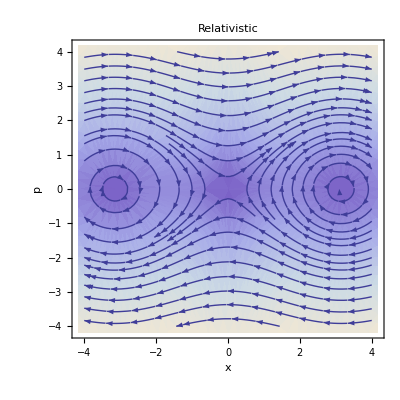

```mathematica
relSPlot[1,3*10^8,sinf,4, 4]
```

```mathematica
Manipulate[
GraphicsRow[{
Animate[
StreamDensityPlot[{(p/m)/Sqrt[1+(p/(m*c))^2],Force[x]},{x,-Domain,Domain},{p,-Range,Range},PlotLabel->"Relativistic", Axes->True,AxesLabel->{x,p}, Epilog->{PointSize->Large,Red,
		Point[
		Table[{x[t]/.First[relPoints[pos[[f]],c,m,Force,1]], p[t]/.First[relPoints[pos[[f]],c,m,Force,1]]} ,{f,1,20}]],PlotRange->{{-4,4},{-4,4}} ,AspectRatio->GoldenRatio}, ImageSize->400,PerformanceGoal->"Speed"],{t,0,1},AnimationRunning->False],
Animate[
StreamDensityPlot[{(p/m),Force[x]},{x,-Domain,Domain},{p,-Range,Range},PlotLabel->"Newtonian", Axes-> True,AxesLabel->{x,p}, Epilog->{PointSize->Large,Red,
		Point[
		Table[{x[t]/.First[relPoints[pos[[f]],c,m,Force,3]], p[t]/.First[relPoints[pos[[f]],c,m,Force,1]]} ,{f,1,20}]],PlotRange->{{-4,4},{-4,4}} ,AspectRatio->GoldenRatio}, ImageSize->400],{t,0,1},AnimationRunning->False]}, ImageSize->1000

], Style["Comparison of Relativistic and Newtonian Momentum Space", 12, Bold],Delimiter,{{c,1,"Speed of Light"},1,3*10^8},{{m,2,"Mass"},1,100},Delimiter,{Force,{hookef, cf, sinf, tanf},ControlType->PopupMenu},Delimiter, {Domain,3,30},{Range,3,30},ContentSize->1000, ContinuousAction->False]
```

```mathematica
Comparison
```

```mathematica
Manipulate[
GraphicsRow[{
Animate[
StreamDensityPlot[{(p/m)/Sqrt[1+(p/(m*c))^2],Force[x]},{x,-Domain,Domain},{p,-Range,Range},PlotLabel->"Relativistic", Axes->True,AxesLabel->{x,p}, Epilog->{PointSize->Large,Red,
		Point[
		Table[{x[t]/.First[relPoints[pos[[f]],c,m,Force,1]], p[t]/.First[relPoints[pos[[f]],c,m,Force,1]]} ,{f,1,20}]],PlotRange->{{-4,4},{-4,4}} ,AspectRatio->GoldenRatio}, ImageSize->400,PerformanceGoal->"Speed"],{t,0,1},AnimationRunning->False],
Animate[
StreamDensityPlot[{(p/m),Force[x]},{x,-Domain,Domain},{p,-Range,Range},PlotLabel->"Newtonian", Axes-> True,AxesLabel->{x,p}, Epilog->{PointSize->Large,Red,
		Point[
		Table[{x[t]/.First[relPoints[pos[[f]],c,m,Force,3]], p[t]/.First[relPoints[pos[[f]],c,m,Force,1]]} ,{f,1,20}]],PlotRange->{{-4,4},{-4,4}} ,AspectRatio->GoldenRatio}, ImageSize->400],{t,0,1},AnimationRunning->False]}, ImageSize->1000

], Style["Comparison of Relativistic and Newtonian Momentum Space", 12, Bold],Delimiter,{{c,1,"Speed of Light"},1,3*10^8},{{m,2,"Mass"},1,100},Delimiter,{Force,{hookef, cf, sinf, tanf},ControlType->PopupMenu},Delimiter, {Domain,3,30},{Range,3,30},ContentSize->1000, ContinuousAction->False]
```

```mathematica
Manipulate[
GraphicsRow[{

Animate[
Graphics[{PointSize->Large, Red, Point[
		Table[{x[t]/.First[relPoints[pos[[f]],c,m,force,1]], p[t]/.First[relPoints[pos[[f]],c,m,force,1]]} ,{f,1,20}]]}]{t,0,1},AnimationRunning->False],
Animate[
Graphics[{PointSize->Large,Red,
		Point[
		Table[{x[t]/.First[relPoints[pos[[f]],c,m,force,3]], p[t]/.First[relPoints[pos[[f]],c,m,force,1]]} ,{f,1,20}]],PlotRange->{{-4,4},{-4,4}} ,AspectRatio->GoldenRatio}, ImageSize->400],{t,0,1},AnimationRunning->False]}],

{{c,1,"Speed of Light"},1,3*10^8},{{m,2,"Mass"},1,100},{force,{hookef, cf, sinf, tanf},ControlType->PopupMenu},{Domain,3,30},{Range,3,30},ContentSize->1000, ContinuousAction->False]
```